# Fully implicit scheme for differential pulse voltammetry

## With Richtmyer modification and expanding space grid.

Version 2.0
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.7]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
(*options for voltammograms*)

optionA={
FrameTicks-> Automatic,
PlotStyle->{Red,AbsoluteThickness[0.7]},
FrameLabel->{
Style["increment",FontFamily->"Arial" ,FontSize-> 12,FontColor->Black],
Style["χ",FontFamily-> "Times New Roman" ,FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
(*options for voltammograms*)

optionB={
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameTicks-> Automatic,
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],
Style["χ",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],
None,
None}
};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeVarDiagonals2];

makeVarDiagonals2[m_Integer,d_][a_]:=
	Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];(*lower diagonal*)
		z=Table[-d*a^(3-2*j),{j,2,m-2}];(*upper diagonal*)
		y=Table[1+(1+a)*d*a^(3-2*j),{j,2,m-1}];(*centre*)
{x,y,z}]

Clear[makeRichtmyerExpDiagonals];

makeRichtmyerExpDiagonals[m_Integer,d_][a_]:=Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];
		z=Table[-d*a^(3-2*j),{j,2,m-2}];
		y=Table[(25./12.+(1.+a)*d*a^(3-2*j)),{j,2,m-1}];
{x,y,z}]
```

```mathematica
Clear[𝔻,a,x,y,z];
{x,y,z}=makeVarDiagonals2[7,𝔻][a]
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,4},{j,4}]//MatrixForm
```

{{-𝔻/a^2,-𝔻/a^4,-𝔻/a^6,-𝔻/a^8},{1+((1+a) 𝔻)/a,1+((1+a) 𝔻)/a^3,1+((1+a) 𝔻)/a^5,1+((1+a) 𝔻)/a^7,1+((1+a) 𝔻)/a^9},{-𝔻/a,-𝔻/a^3,-𝔻/a^5,-𝔻/a^7}}

(1+((1+a) 𝔻)/a | -𝔻/a | 0 | 0
-𝔻/a^2 | 1+((1+a) 𝔻)/a^3 | -𝔻/a^3 | 0
0 | -𝔻/a^4 | 1+((1+a) 𝔻)/a^5 | -𝔻/a^5
0 | 0 | -𝔻/a^6 | 1+((1+a) 𝔻)/a^7)

```mathematica
Clear[𝔻,a,x,y,z];
{x,y,z}=makeRichtmyerExpDiagonals[7,𝔻][a]
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,4},{j,4}]//MatrixForm
```

{{-𝔻/a^2,-𝔻/a^4,-𝔻/a^6,-𝔻/a^8},{2.08333+((1.+a) 𝔻)/a,2.08333+((1.+a) 𝔻)/a^3,2.08333+((1.+a) 𝔻)/a^5,2.08333+((1.+a) 𝔻)/a^7,2.08333+((1.+a) 𝔻)/a^9},{-𝔻/a,-𝔻/a^3,-𝔻/a^5,-𝔻/a^7}}

(2.08333+((1.+a) 𝔻)/a | -𝔻/a | 0 | 0
-𝔻/a^2 | 2.08333+((1.+a) 𝔻)/a^3 | -𝔻/a^3 | 0
0 | -𝔻/a^4 | 2.08333+((1.+a) 𝔻)/a^5 | -𝔻/a^5
0 | 0 | -𝔻/a^6 | 2.08333+((1.+a) 𝔻)/a^7)

## Set Up Solution

```mathematica
Clear[implicitExpDPP];

implicitExpDPP[m_Integer,n_Integer,d_,{upperLimit_,ksStar_,α_,ΔEs_,ΔEp_,ts_,tw_},a_]:=Module[{x,y,z,len,mat,y1,z1,initial,solveNext},

{x,y,z}=makeVarDiagonals2[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,u},
u[j_]=UnitStep[(j-tw)(j-ts)(j-ts-100)];

ξ=Exp[upperLimit-(ΔEs/ts)*(k-Mod[k,ts])-ΔEp*u[Mod[k,ts]]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦-1⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]
];
Rest@FoldList[solveNext,initial,Range[0,n]]
]
```

```mathematica
Clear[implicitExpRichtmeyerDPP];

implicitExpRichtmeyerDPP[m_Integer,n_Integer,d_,{upperLimit_,ksStar_,α_,ΔEs_,ΔEp_,ts_,tw_},a_]:=Module[{x,y,z,len,mat,y1,z1,initial,c,solveStart,solveRest},

{x,y,z}=makeVarDiagonals2[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveStart[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,u},
u[j_]=UnitStep[(j-tw)(j-ts)(j-ts-100)];

ξ=Exp[upperLimit-(ΔEs/ts)*(k-Mod[k,ts])-ΔEp*u[Mod[k,ts]]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦m-2⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]
];
c=FoldList[solveStart,initial,Range[0,5]];

{x,y,z}=makeRichtmyerExpDiagonals[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;

solveRest[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,u},
u[j_]=UnitStep[(j-tw)(j-ts)(j-ts-100)];
ξ=Exp[upperLimit-(ΔEs/ts)*(k-Mod[k,ts])-ΔEp*u[Mod[k,ts]]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=Flatten@MapThread[{4*#4-3*#3+(4./3.)*#2-0.25*#1}&,Take[list,-4]];
b=b⟦2;;-2⟧;
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦-1⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
Join[list,{Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]}]
];

Rest@Fold[solveRest,c,Range[6,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f,𝒟];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)
f=F/(R*T);
𝒟=1.*^-5;(*diffusion coefficient*)
```

### Electrochemical variables

```mathematica
Clear[α,ks,ΔEs,ΔEp,upperLimit,𝕥];α=0.5;
 
(*transfer coefficient*)

ks=1.*^3;(*standard rate constant*)

ΔEs=f*0.005;(*staircase dimensionless step size*)

ΔEp=f*0.05;(*dimensionless pulse size*)

upperLimit=10.;(*initial potential versus the formal potential*)

𝕥=20.;(*dimensionless potential range required*)
```

### Simulation variables

```mathematica
Clear[𝔻,pulses,p,ts,pulseWidth,tw,n,a,temp,m,τ,ksStar,conc,y1,z1,c];

𝔻=2.;(*model diffusion coefficient*)

pulses=Round[𝕥/ΔEs];(*number of pulses*)

ts=100;(*length of pulse plus length of rest time*)

p=5;(*length of the pulse*)

tw=ts-p;

n=pulses*ts;

a=1.1;(*grid expansion factor*)
temp=Solve[∑_(j=1)^(mm-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),mm,InverseFunctions-> True];

m=Ceiling[mm/.temp⟦1⟧];(*number of spacial grid points*)

τ=𝕥/n; (*calculation of the incremental potential step*)

ksStar=2.ks*Sqrt[1./(Pi*𝔻*(p-1))];(*dimensionless rate constant*)
```

```mathematica
{α,ks,Δ𝔼p,upperLimit,𝕥,𝔻,pulses,p,tL,n,a,m,τ,ksStar}
```

{0.5,1000.,Δ𝔼p,10.,20.,2.,103,5,tL,10300,1.1,49,0.00194175,398.942}

## Show waveform

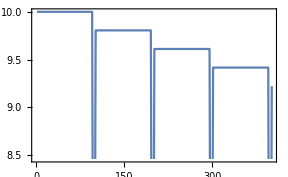

{95,5,95,5,95,5,95,5,1}

```mathematica
u[j_]:=UnitStep[(j-tw)(j-ts)(j-ts-100)];

diffPulse=Table[upperLimit-(ΔEs/ts)*(k-Mod[k,ts])-ΔEp*u[Mod[k,ts]],{k,0,400}];

ListPlot[diffPulse]

Length/@Split[diffPulse]
```

## Fully implicit differential pulse voltammogram

For a fully implicit solution execute the cell below:

```mathematica
c=implicitExpDPP[m,n,𝔻,{upperLimit,ksStar,α,ΔEs,ΔEp,ts,tw},a];
```

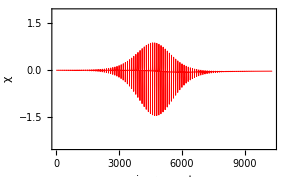

```mathematica
dpv1=Map[(((2.+a)*a*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)*√((Pi*𝔻*(p-1))/(2.*a^2*(1.+a))))&,c];

plot1=ListPlot[dpv1,optionA,PlotRange-> {{0,n},{Min[dpv1]-1,Max[dpv1]+1}}]
```

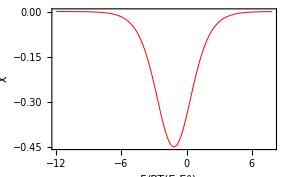

```mathematica
start=Table[dpv1⟦k⟧,{k,tw,Length[dpv1],ts}];

end=Table[dpv1⟦k⟧,{k,ts,Length[dpv1],ts}];

difference=Table[{upperLimit-ΔEp-(k*ΔEs),end⟦k⟧-start⟦k⟧},{k,1,Length[end]}];

diffPlot=ListPlot[difference,optionB,PlotStyle-> {Red}]
```

```mathematica
Min[difference⟦All,2⟧]
```

-0.448179

Alternatively you can find the peak height by Interpolation.

```mathematica
Clear[interpData,peakFind,peak,x];

interpData=Interpolation[difference];

peakFind=Partition[Flatten[FindMinimum[interpData[x], {x,2,-2}]],2];

(*peak potential less than .01 is rounded to zero*)
 
peak={Chop[x/. #⟦2⟧,.01],-#⟦1⟧}& /@ peakFind
```

{{-1.16653,0.448661}}

## FIRM differential pulse voltammogram

For a Fully Implicit solution with Richtmyer Modification execute the cell below:

```mathematica
c=implicitExpRichtmeyerDPP[m,n,𝔻,{upperLimit,ksStar,α,ΔEs,ΔEp,ts,tw},a];
```

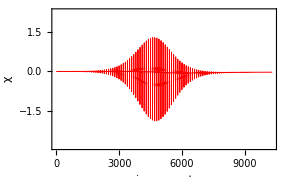

```mathematica
dpv1=Map[(((2.+a)*a*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)*√((Pi*𝔻*(p-1))/(2.*a^2*(1.+a))))&,c];

plot1=ListPlot[dpv1,optionA,PlotRange-> {{0,n},{Min[dpv1]-1,Max[dpv1]+1}}]
```

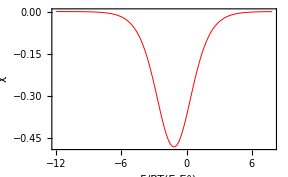

```mathematica
start=Table[dpv1⟦k⟧,{k,tw,Length[dpv1],ts}];

end=Table[dpv1⟦k⟧,{k,ts,Length[dpv1],ts}];

difference=Table[{upperLimit-ΔEp-(k*ΔEs),end⟦k⟧-start⟦k⟧},{k,1,Length[end]}];

diffPlot=ListPlot[difference,optionB,PlotStyle-> {Red}]
```

```mathematica
Min[difference⟦All,2⟧]
```

-0.483178

Alternatively you can find the peak height by Interpolation.

```mathematica
Clear[interpData,peakFind,peak,xx];

interpData=Interpolation[difference];

peakFind=Partition[Flatten[FindMinimum[interpData[xx], {xx,2,-2}]],2];

(*peak potential less than .01 is rounded to zero*)
 
peak={Chop[xx/. #⟦2⟧,.01],-#⟦1⟧}& /@ peakFind
```

{{-1.16672,0.483701}}